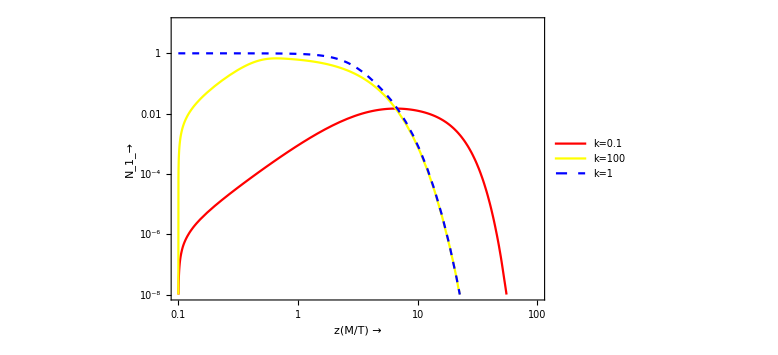

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
k=1;
solution= NDSolve[{Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]+(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

k=100;
solution1= NDSolve[{Nn1'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), 
Nl1'[z]== -(1/2)*(z *k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn1[1z]+(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==0, Nl1[0.1]==10^-7}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];
k=0.01;
solution2= NDSolve[{Nn2'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]),
 Nl2'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] +ϵ*(z *k)* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]+(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==0, Nl2[0.1]==10^-7}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[Evaluate[Nn[z]/.solution],{z, 0.1,100},PlotRange->{{0.1,100},{10^-8,10}}, Frame-> True,PlotStyle->{Blue, Dashed},PlotLegends->{"k=1"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn1[z]/.solution1],{z, 0.1,100}, PlotRange->{{0.1,100},{10^-8,10}},Frame-> True,PlotStyle->Yellow,  PlotLegends->{"k=100"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn2[z]/.solution2],{z, 0.1,100}, PlotRange->{{0.1,100},{10^-8,10}},Frame-> True,PlotStyle->Red, PlotLegends->{"k=0.1"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%]
```

```mathematica
Parameters={Γ->10^-12  , g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
 M=  1000;
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

 M= 100;
solution1= NDSolve[{Nn1'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nl1'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-3, Nl1[0.1]==10^-7}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];
 M=10000;
solution2= NDSolve[{Nn2'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nl2'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==10^-6, Nl2[0.1]==10^-7}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[Evaluate[Nn[z]/.solution],{z, 0.1,200},PlotRange->{{0.1,300},{10^-8,10}}, Frame-> True,PlotStyle->{Blue, Dashed},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn1[z]/.solution1],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Yellow,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_l_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn2[z]/.solution2],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%]
```

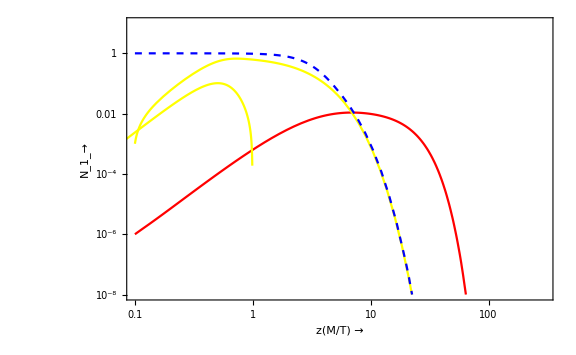
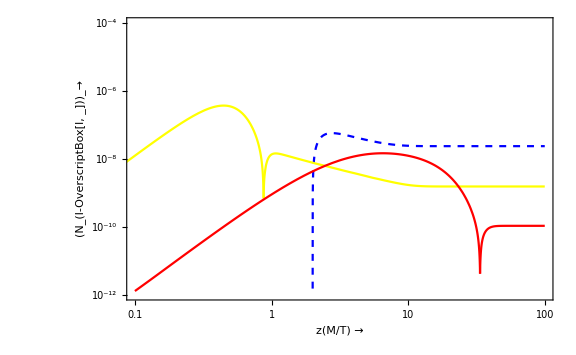

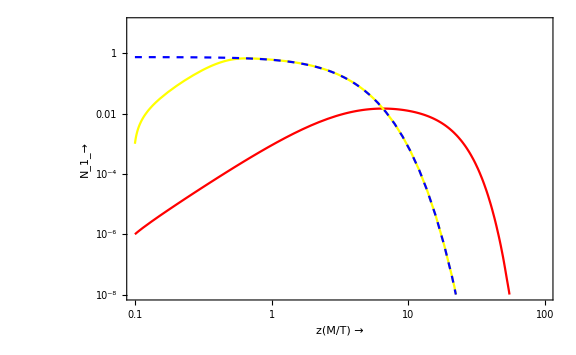

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
k=1;
solution= NDSolve[{Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

k=100;
solution1= NDSolve[{Nn1'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), 
Nl1'[z]== -(1/2)*(z *k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-3, Nl1[0.1]==10^-7}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];
k=0.01;
solution2= NDSolve[{Nn2'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]),
 Nl2'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] +ϵ*(z *k)* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==10^-6, Nl2[0.1]==10^-7}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[(3/8)*z^2*BesselK[2,z],{z, 0.1,100},PlotRange->{{0.1,100},{10^-8,10}}, Frame-> True,PlotStyle->{Blue, Dashed},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn1[z]/.solution1],{z, 0.1,100}, PlotRange->{{0.1,100},{10^-8,10}},Frame-> True,PlotStyle->Yellow, FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn2[z]/.solution2],{z, 0.1,100}, PlotRange->{{0.1,100},{10^-8,10}},Frame-> True,PlotStyle->Red, FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];

Show[%,%%,%%%]
```

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl, z]
k=0.01;
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-6, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 100}];
bc=Evaluate[Nn[33.6]/.solution];
bc1=Evaluate[Nl[33.6]/.solution];
solution1= NDSolve[{
Nn'[z]== -z * k * (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[33.6]==bc, Nl[33.6]==bc1}/.Parameters,{Nn, Nl},{z,33.6,  100},PrecisionGoal->3];
LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,33.6}, PlotRange->{{0.1,100},{10^-12,10^-4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nl[z]/.solution1],{z,33.6,100}, PlotRange->{{0.1,100},{10^-12,10^-4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%]
```

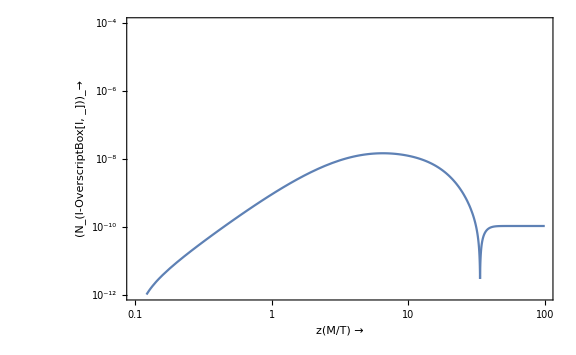

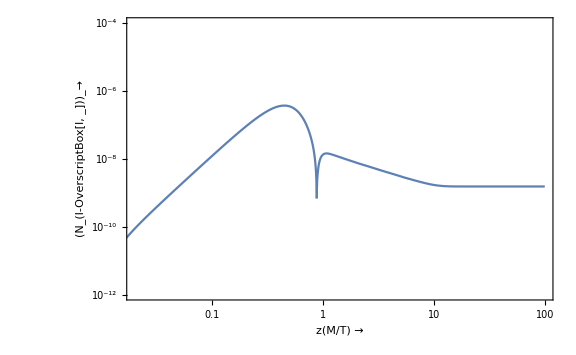

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl, z]
k=100;
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-3, Nl[0.01]==0}/.Parameters,{Nn, Nl},{z, 0.01, 0.875}];
bc=Evaluate[Nn[0.875]/.solution];
bc1=Evaluate[Nl[0.875]/.solution];
solution1= NDSolve[{
Nn'[z]== -z * k * (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.875]==bc, Nl[0.875]==bc1}/.Parameters,{Nn, Nl},{z,0.875,  100},PrecisionGoal->3];
LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.01,0.875}, PlotRange->{{0.02,100},{10^-12,10^-4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nl[z]/.solution1],{z,0.875,100}, PlotRange->{{0.02,100},{10^-12,10^-4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%]
```

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1, Nl1, z, k ,k1]
k=0.01;
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-6, Nl[0.01]==0}/.Parameters,{Nn, Nl},{z, 0.01, 100}];
Evaluate[(Nn[2]-(3/8)*20^2*BesselK[2,2])/.solution]
```

{-38.0597}

{0.644561}

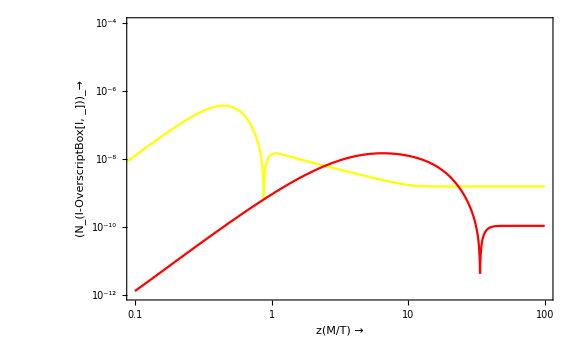

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1, Nl1, z, k ,k1]
k=0.01;
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-6, Nl[0.01]==0}/.Parameters,{Nn, Nl},{z, 0.01, 100}];
bc=Evaluate[Nn[33.6]/.solution];
bc1=Evaluate[Nl[33.6]/.solution];
solution1= NDSolve[{
Nn'[z]== -z * k * (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[33.6]==bc, Nl[33.6]==bc1}/.Parameters,{Nn, Nl},{z,33.6,  100},PrecisionGoal->3];

Clear[z]
k1=100;
solution2= NDSolve[{
Nn1'[z]== -z * k1* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), 
Nl1'[z]== -(1/2)*(z * k1* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] -ϵ*(z * k1)* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-3, Nl1[0.01]==0}/.Parameters,{Nn1, Nl1},{z, 0.01, 0.875}];
bc2=Evaluate[Nn1[0.875]/.solution2]
bc3=Evaluate[Nl1[0.875]/.solution2];
solution3= NDSolve[{
Nn1'[z]== -z * k1* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nl1'[z]== -(1/2)*(z * k1* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * k1)* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.875]==bc2, Nl1[0.875]==bc3}/.Parameters,{Nn1, Nl1},{z,0.875,  100},PrecisionGoal->3];



LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,33.6}, PlotRange->{{0.02,100},{10^-12,10^-4}},Frame-> True,PlotStyle->Red,FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nl[z]/.solution1],{z,33.6,100},  PlotRange->{{0.02,100},{10^-12,10^-4}},Frame-> True,PlotStyle->Red,FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

LogLogPlot[Evaluate[Nl1[z]/.solution2],{z,0.01,0.875}, PlotRange->{{0.1,100},{10^-12,10^-4}},Frame-> True,PlotStyle->Yellow,FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nl1[z]/.solution3],{z,0.875,100}, PlotRange->{{0.1,100},{10^-12,10^-4}},Frame-> True,PlotStyle->Yellow,FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
Show[%,%%, %%%,%%%%]
```

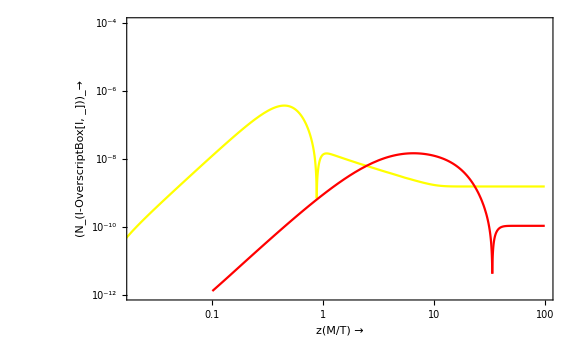
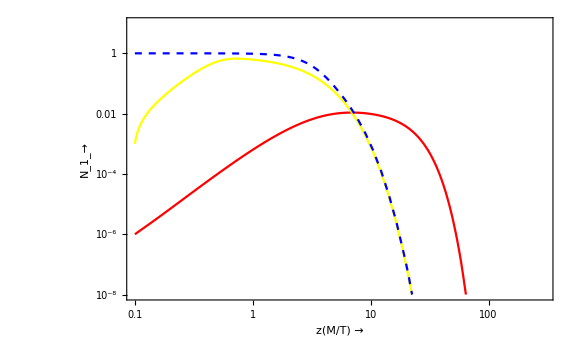

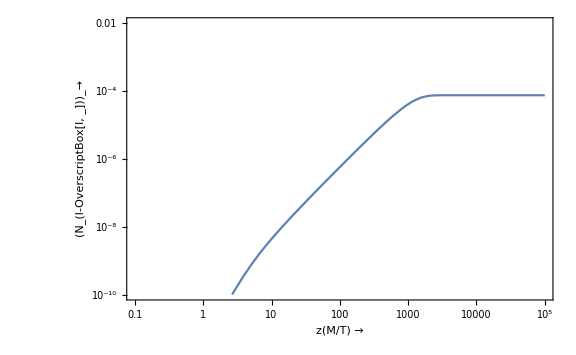

```mathematica
Parameters={Γ->10^-16.7  , g-> 106.75 , M->  5000, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ*0.5/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==3/4, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 10^5}];

LogLogPlot[Evaluate[Abs[Nl[z]]/.solution],{z,0.1,10^5}, PlotRange->{{0.1,10^5},{10^-10,10^-2}},GridLines->{{3.8,38.2,382,3820,38200},{10^-7}},GridLinesStyle->Directive[Red, Dashed] ,Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

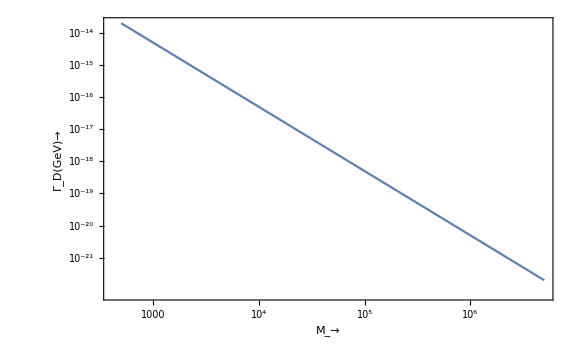

```mathematica
ListLogLogPlot[{{500,10^-13.7},{5000,10^-15.7},{50000,10^-17.7},{500000,10^-19.7},{5000000, 10^-21.7}},Joined->True, PlotRange->All,  Frame-> True,FrameTicksStyle->Directive[Black,15],FrameLabel->{" M_→","Γ_D(GeV)→"},LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large]
```

```mathematica
3/8 BesselK[2,1]
```

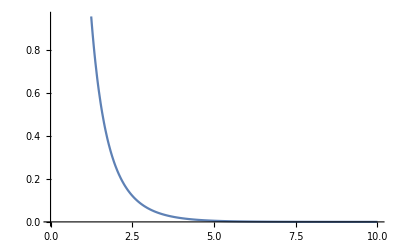

```mathematica
Plot[BesselK[2,z],{z,0,10}]
```

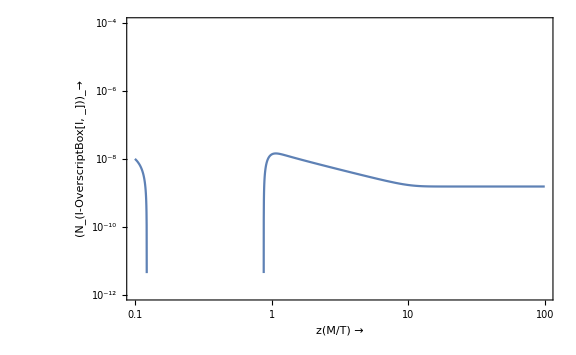

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl, z]
k=100;
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-3, Nl[0.1]==10^-8}/.Parameters,{Nn, Nl},{z, 0.1, 100}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,100}, PlotRange->{{0.1,100},{10^-12,10^-4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
(3/8)*0.1^2*BesselK[2,0.1]
```

0.74814

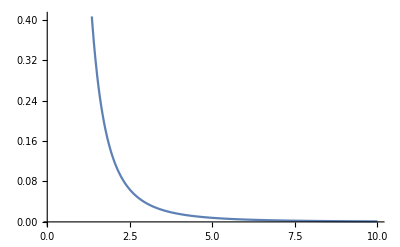

```mathematica
Plot[z^-3, {z,0.1,10}]
```

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
k=1;
solution= NDSolve[{Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]+(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn, Nl},{z, 0.1, 200}];

k=100;
solution1= NDSolve[{Nn1'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), 
Nl1'[z]== -(1/2)*(z *k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn1[1z]+(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-3, Nl1[0.1]==10^-7}/.Parameters,{Nn1, Nl1},{z, 0.1, 200}];
Evaluate[Nn[1]/.solution]
Evaluate[Nn1[1]/.solution1]
```

{0.957341}

{0.615659}

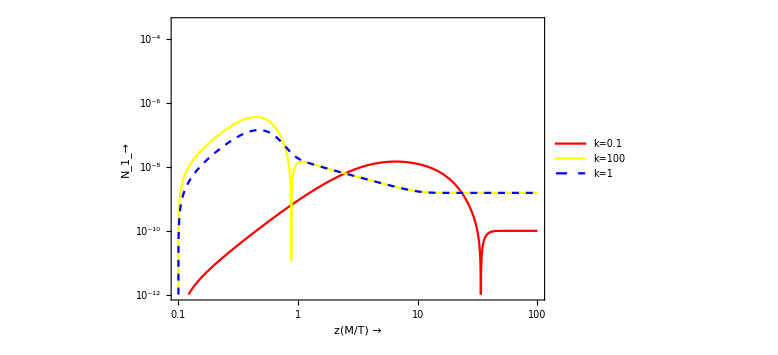

```mathematica
Parameters={ g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
k=100;
solution= NDSolve[{Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

k=100;
solution1= NDSolve[{Nn1'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), 
Nl1'[z]== -(1/2)*(z *k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-6, Nl1[0.1]==0}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];
k=0.01;
solution2= NDSolve[{Nn2'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]),
 Nl2'[z]== -(1/2)*(z * k)* (BesselK[1,z]/BesselK[2,z])*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] -ϵ*(z *k)* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==10^-6, Nl2[0.1]==0}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[Evaluate[Abs[Nl[z]]/.solution],{z, 0.1,100},PlotRange->{{0.1,100},{10^-12,10^-3.5}}, Frame-> True,PlotStyle->{Blue, Dashed},PlotLegends->{"k=1"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Abs[Nl1[z]]/.solution1],{z, 0.1,100},PlotRange->{{0.1,100},{10^-12,10^-3.5}},Frame-> True,PlotStyle->Yellow,  PlotLegends->{"k=100"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Abs[Nl2[z]]/.solution2],{z, 0.1,100},PlotRange->{{0.1,100},{10^-12,10^-3.5}},Frame-> True,PlotStyle->Red, PlotLegends->{"k=0.1"},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%]
```

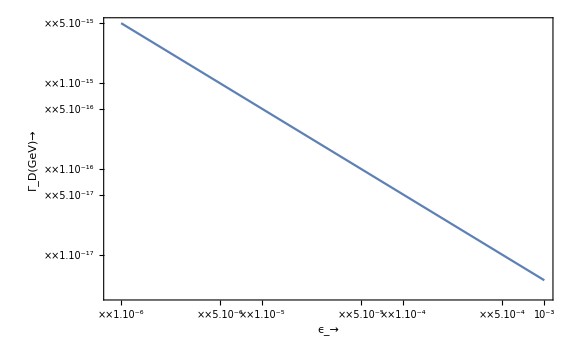

```mathematica
ListLogLogPlot[{{10^-3,10^-17.3},{10^-4,10^-16.3},{10^-5,10^-15.3},{10^-6,10^-14.3}},Joined->True, PlotRange->All,  Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ_D(GeV)→"},LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large]
```

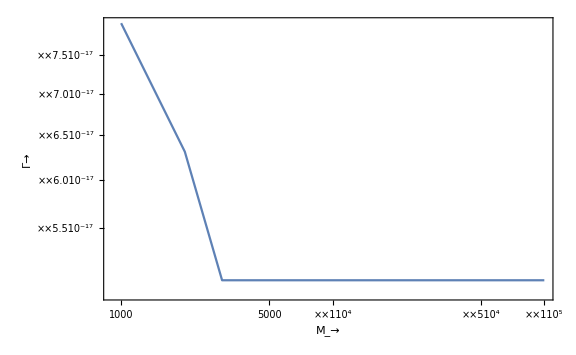

```mathematica
ListLogLogPlot[{{10^3,10^-16.1},{2000,10^-16.2},{3000,10^-16.3},{10^4,10^-16.3},{10^5,10^-16.3}},Joined->True, PlotRange->All,  Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" M_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```